# Análisis

## Separados por personas

People=10,100,1000
Time={20-100},{100-1000},{1000-10000}
Capacity={2-10}

```mathematica
SetDirectory[NotebookDirectory[]];
```

## Variables:

exTimes es la cantidad de ejecuciones que se realizaron, las carpetas con los grafos debén estar nombradas con los números desde el 1 hasta exTimes

```mathematica
peopleVals={10,100,1000};
capacity=Range[2,10,2];
timeVals=Range[2,10,2];
avClustering={};
avApl={};
sDClustering={};
sDApl={};
exTimes=80;
clustering100={};
apl100={};
graphicAttributes={PlotMarkers-> {Automatic,5},Frame->{True,True,True,True},GridLines->Automatic,GridLinesStyle->Directive[Gray,Dotted],FrameStyle->{Directive[Black],Directive[Black],Directive[Gray],Directive[Gray]},TicksStyle->Directive[7],PlotStyle->{Red,{Red,Dashed},Orange,{Orange,Dashed},{Orange,Dotted}}};
```

## Funciones para la importación de los grafos y el calculo de las medidas

```mathematica
ClearVals:=Module[{},
peopleVals={10,100,1000};
capacity=Range[2,10,2];
timeVals=Range[2,10,2];
avClustering={};
avApl={};
sDClustering={};
sDApl={};
exTimes=80;
];
```

### Funciones para importar los grafos:

Retorna una lista de largo exTimes, donde todas las redes tienen la configuración people=amountPeople, capacity=i, time=j

```mathematica
ImportGraphs[amountPeople_,i_,j_]:=
Table[Import[StringJoin["graphs/model-v3/",IntegerString[exNumber],"/","network-",IntegerString[amountPeople],"-",IntegerString[capacity[[i]]],"-",IntegerString[timeVals[[j]]*amountPeople],".g6"]],{exNumber,1,exTimes,1}];
```

Retorna una lista con los grafos de cada capacidad para people=amountPeople en el caso de 100.000 unidades de tiempo

```mathematica
ImportLastGraphs[amountPeople_]:=Table[Import[StringJoin["graphs/model-v3/","network-",IntegerString[amountPeople],"-",IntegerString[capacity[[i]]],"-100000.g6"]],{i,1,Length[capacity],1}];
```

### Función para calcular el promedio y la desviación estándar del clustering coefficient y del average path length:

No retorna nada, agrega un elemento a cada lista avClustering, avApl, sDClustering, sDApl. Correspondiendo al promedio y desviación estándar de las medidas de todas las redes con la configuración people=amountPeople, capacity=i, time=j

```mathematica
CalulateVals[amountPeople_,i_,j_]:=Module[{listClustering,meanClustering,sdClustering,listApl,meanApl,sdApl,networks},
networks=ImportGraphs[amountPeople,i,j];

listClustering=Map[GlobalClusteringCoefficient,networks];
meanClustering=Mean[listClustering];
sdClustering=StandardDeviation[listClustering];

listApl=Map[MeanGraphDistance,networks];
listApl=DeleteCases[listApl,Infinity];
meanApl=Mean[listApl];
sdApl=StandardDeviation[listApl];

avClustering=Append[avClustering,meanClustering];
sDClustering=Append[sDClustering,sdClustering];
avApl=Append[avApl,meanApl];
sDApl=Append[sDApl,sdApl];
];
```

Agrega a clustering100 y apl100 los valores de las medidas correspondientes para una cantidad de personas determinada

```mathematica
CalculateVals100[amountPeople_]:=Module[{networks,listCl,listApl},
networks=ImportLastGraphs[amountPeople];

listCl=Map[GlobalClusteringCoefficient,networks];
listApl=Map[MeanGraphDistance,networks];

clustering100=Append[clustering100,listCl];
apl100=Append[apl100,listApl];
];
```

### Función para calcular todas las configuraciones tiempo - capacidad:

```mathematica
AverageVals[amountPeople_]:=Module[{},
Do[CalulateVals[amountPeople,i,j],{i,1,Length[capacity],1},{j,1,Length[timeVals],1}];
];
```

Para calcular todas las cantidades de personas para las 100.000 unidades de tiempo

```mathematica
Vals100[]:=
Do[CalculateVals100[peopleVals[[i]]],{i,1,Length[peopleVals],1}];
```

## Funciones para las graficas

### Funciones para asignar los textos (k=# o people=#) para el clustering coefficient

```mathematica
AssignTextsCl[amountPeople_]:=Module[{texts,clustering},
Switch[amountPeople,
10, clustering=avClustering10,
100,clustering=avClustering100,
1000,clustering=avClustering1000
];
texts=Table[Text[Style[StringJoin["k=",IntegerString[capacity[[i]]]],10],{amountPeople  (timeVals[[Length[timeVals]]]-0.2),clustering[[i,5]]+0.02}],{i,1,Length[capacity],1}];
Graphics[texts,Ticks->None]
];
```

```mathematica
AssignTextsPeople[type_]:=Module[{posY,texts,vals},
Switch[type,
"Cl",posY=0.02;vals=clustering100,
"Apl",posY=-0.02;vals=apl100
];
texts=Table[Text[Style[StringJoin["people=",IntegerString[peopleVals[[i]]]],10],{ capacity[[Length[capacity]]]-0.2,vals[[i,5]]+posY}],{i,1,Length[peopleVals],1}];
Graphics[texts,Ticks->None]
];
```

### Función para asignar los textos (k=#) para el average path length

```mathematica
AssignTextsApl[amountPeople_]:=Module[{texts,apl},
Switch[amountPeople,
10, apl=avApl10,
100,apl=avApl100,
1000,apl=avApl1000
];
texts=Table[Text[Style[StringJoin["k=",IntegerString[capacity[[i]]]],10],{amountPeople  (timeVals[[Length[timeVals]]]-0.2),apl[[i,5]]-0.02}],{i,1,Length[capacity],1}];
For[i=Length[capacity],i>0,i--,
If[Count[Flatten[apl[[i]]],_Rational]==0,
texts=Delete[texts,i]
];
];
Graphics[texts,Ticks->None]
];
```

### Función para asignar el rango del gráfico para el clustering coefficient

```mathematica
AssignPlotRangeCl[amountPeople_]:=Module[{clustering},
Switch[amountPeople,
10, clustering=avClustering10,
100,clustering=avClustering100,
1000,clustering=avClustering1000
];
PlotRange->{Automatic,{Min[clustering],Max[clustering]+0.05}}
]
```

### Función para asignar el rango del gráfico para el average path length

```mathematica
AssignPlotRangeApl[amountPeople_]:=Module[{apl,validVals},
Switch[amountPeople,
10, apl=avApl10,
100,apl=avApl100,
1000,apl=avApl1000
];
validVals=Cases[Flatten[apl],_Rational];
PlotRange->{Automatic,{Min[validVals]-0.05,Max[validVals]}}
]
```

```mathematica
AssignplotRange100[type_]:=Module[{validVals},
Switch[type,
"Cl",PlotRange->{Automatic,{Min[clustering100],Max[clustering100]+0.05}},
"Apl", validVals=Cases[Flatten[apl100],_Rational];
PlotRange->{Automatic,{Min[validVals]-0.05,Max[validVals]}}
]
];
```

### Función para asignar las etiquetas de los ejes

los valores posibles para type son "Cl" o "Apl"

```mathematica
AssignFrameLabel[type_]:=
Switch[type,
"Cl",FrameLabel->{Style["Time",12,Black],Style["(av) Clustering Coefficient_80",12,Black]},
"Apl",FrameLabel->{Style["Time",12,Black],Style["(av) Average Path Length_80",12,Black]}
]
```

### Función para asignar el nombre del gráfico

los valores posibles para type son “Cl” o “Apl”, para el caso de los 100.000 unidades de tiempo se pasa 100.000 a amountPeople

```mathematica
AssignName[type_,amountPeople_]:=
Switch[type,
"Cl",StringJoin["cc-",IntegerString[amountPeople],".pdf"],
"Apl",StringJoin["apl-",IntegerString[amountPeople],".pdf"]
]
```

## People=10

### Sacar los valores del clustering y del apl

```mathematica
ClearVals;
AverageVals[10];
avClustering10=avClustering;
avApl10=avApl;
sDClustering10=sDClustering;
sDApl10=sDApl;
```

### Clustering coefficient

```mathematica
avClustering10=Partition[avClustering10,5];
```

#### capacity vs clustering coefficient

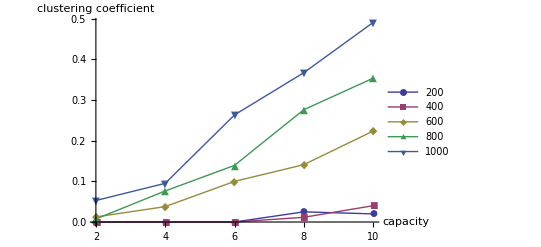

```mathematica
dataPlotCl101=Table[Table[{capacity[[k]],avClustering10[[k,t]]},{k,1,Length[capacity],1}],{t,1,Length[timeVals],1}];
ListLinePlot[dataPlotCl101,PlotLegends->100timeVals,AxesLabel->{"capacity","clustering coefficient"},PlotMarkers->Automatic]
```

#### time vs clustering coefficient

```mathematica
dataPlotCl102=Table[Table[{10timeVals[[t]],avClustering10[[k,t]]},{t,1,Length[timeVals],1}],{k,1,Length[capacity],1}];
Export[AssignName["Cl",10],Show[ListLinePlot[dataPlotCl102,AssignFrameLabel["Cl"],AssignPlotRangeCl[10],graphicAttributes],AssignTextsCl[10]]];
```

### Average path length

```mathematica
avApl10=Partition[avApl10,5];
```

#### capacity vs apl

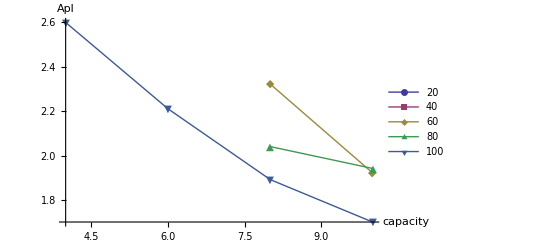

```mathematica
dataPlotApl101=Table[Table[{capacity[[k]],avApl10[[k,t]]},{k,1,Length[capacity],1}],{t,1,Length[timeVals],1}];
ListLinePlot[dataPlotApl101,PlotLegends->10timeVals,AxesLabel->{"capacity","Apl"},PlotMarkers->Automatic]
```

#### time vs apl

```mathematica
dataPlotApl102=Table[Table[{10timeVals[[t]],avApl10[[k,t]]},{t,1,Length[timeVals],1}],{k,1,Length[capacity],1}];
Export[AssignName["Apl",10],Show[ListLinePlot[dataPlotApl102,AssignFrameLabel["Apl"],AssignPlotRangeApl[10],graphicAttributes],AssignTextsApl[10]]];
```

## People=100

### Sacar los valores del clustering y del apl

```mathematica
ClearVals;
AverageVals[100];
avClustering100=avClustering;
avApl100=avApl;
sDClustering100=sDClustering;
sDApl100=sDApl;
```

### Clustering coefficient

```mathematica
avClustering100=Partition[avClustering100,5];
```

#### capacity vs clustering coefficient

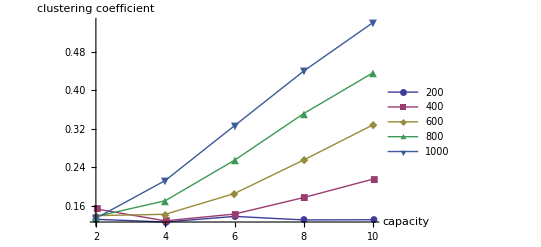

```mathematica
dataPlotCl1001=Table[Table[{capacity[[k]],avClustering100[[k,t]]},{k,1,Length[capacity],1}],{t,1,Length[timeVals],1}];
ListLinePlot[dataPlotCl1001,PlotLegends->100timeVals,AxesLabel->{"capacity","clustering coefficient"},PlotMarkers->Automatic]
```

#### time vs clustering coefficient

```mathematica
dataPlotCl1002=Table[Table[{100timeVals[[t]],avClustering100[[k,t]]},{t,1,Length[timeVals],1}],{k,1,Length[capacity],1}];
Export[AssignName["Cl",100],Show[ListLinePlot[dataPlotCl1002,AssignFrameLabel["Cl"],AssignPlotRangeCl[100],graphicAttributes],AssignTextsCl[100]]];
```

### Average path length

```mathematica
avApl100=Partition[avApl100,5];
```

#### capacity vs apl

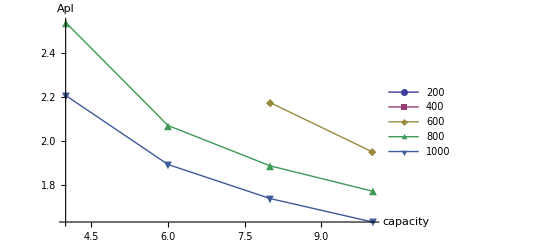

```mathematica
dataPlotApl1001=Table[Table[{capacity[[k]],avApl100[[k,t]]},{k,1,Length[capacity],1}],{t,1,Length[timeVals],1}];
ListLinePlot[dataPlotApl1001,PlotLegends->100timeVals,AxesLabel->{"capacity","Apl"},PlotMarkers->Automatic]
```

#### time vs apl

```mathematica
dataPlotApl1002=Table[Table[{100timeVals[[t]],avApl100[[k,t]]},{t,1,Length[timeVals],1}],{k,1,Length[capacity],1}];
Export[AssignName["Apl",100],Show[ListLinePlot[dataPlotApl1002,AssignFrameLabel["Apl"],AssignPlotRangeApl[100],graphicAttributes],AssignTextsApl[100]]];
```

## People=1000

### Sacar los valores del clustering y del apl

```mathematica
ClearVals;
AverageVals[1000];
avClustering1000=avClustering;
avApl1000=avApl;
sDClustering1000=sDClustering;
sDApl1000=sDApl;
```

### Clustering coefficient

```mathematica
avClustering1000=Partition[avClustering1000,5];
```

#### capacity vs clustering coefficient

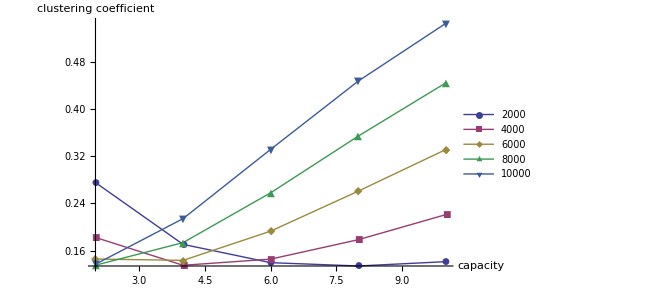

```mathematica
dataPlotCl10001=Table[Table[{capacity[[k]],avClustering1000[[k,t]]},{k,1,Length[capacity],1}],{t,1,Length[timeVals],1}];
ListLinePlot[dataPlotCl10001,PlotLegends->1000timeVals,AxesLabel->{"capacity","clustering coefficient"},PlotMarkers->Automatic]
```

#### time vs clustering coefficient

```mathematica
dataPlotCl10002=Table[Table[{1000timeVals[[t]],avClustering1000[[k,t]]},{t,1,Length[timeVals],1}],{k,1,Length[capacity],1}];
Export[AssignName["Cl",1000],Show[ListLinePlot[dataPlotCl10002,AssignFrameLabel["Cl"],AssignPlotRangeCl[1000],graphicAttributes],AssignTextsCl[1000]]];
```

### Average path length

```mathematica
avApl1000=Partition[avApl1000,5];
```

#### capacity vs apl

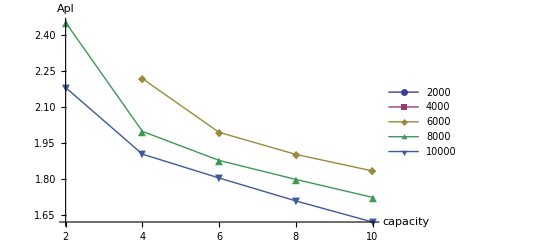

```mathematica
dataPlotApl10001=Table[Table[{capacity[[k]],avApl1000[[k,t]]},{k,1,Length[capacity],1}],{t,1,Length[timeVals],1}];
ListLinePlot[dataPlotApl10001,PlotLegends->1000timeVals,AxesLabel->{"capacity","Apl"},PlotMarkers->Automatic]
```

#### time vs apl

```mathematica
dataPlotApl10002=Table[Table[{1000timeVals[[t]],avApl1000[[k,t]]},{t,1,Length[timeVals],1}],{k,1,Length[capacity],1}];
Export[AssignName["Apl",1000],Show[ListLinePlot[dataPlotApl10002,AssignFrameLabel["Apl"],AssignPlotRangeApl[1000],graphicAttributes],AssignTextsApl[1000]]];
```